NDSolve::dsvar: 0.000204082 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of {x'[t]==x[t]-x[t]^3-3 y[t],x[0]==1,y[0]==1}[-0.5] in the first argument {{x'[t]==x[t]-x[t]^3-3 y[t],x[0]==1,y[0]==1}[-0.5],{y'[t]==3 x[t]+y[t]+2 y[t]^3,x[0]==1,y[0]==1}[-0.5],x[0]==-2.,y[0]==-2.}.

NDSolve::deqn: Equation or list of equations expected instead of {x'[t]==x[t]-x[t]^3-3 y[t],x[0]==1,y[0]==1}[-0.5] in the first argument {{x'[t]==x[t]-x[t]^3-3 y[t],x[0]==1,y[0]==1}[-0.5],{y'[t]==3 x[t]+y[t]+2 y[t]^3,x[0]==1,y[0]==1}[-0.5],x[0]==-2.,y[0]==-1.5}.

NDSolve::deqn: Equation or list of equations expected instead of {x'[t]==x[t]-x[t]^3-3 y[t],x[0]==1,y[0]==1}[-0.5] in the first argument {{x'[t]==x[t]-x[t]^3-3 y[t],x[0]==1,y[0]==1}[-0.5],{y'[t]==3 x[t]+y[t]+2 y[t]^3,x[0]==1,y[0]==1}[-0.5],x[0]==-2.,y[0]==-1.}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

{{y→InterpolatingFunction[…]}}

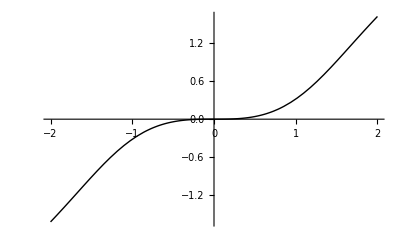

```mathematica
ClearAll["Global`*"]
f[x_, y_] := x^2 - y^2
Clear[y]
NDSolve[{y'[x]==f[x,y[x]],y[0]==0},y,{x,-2,2}]
graph=Plot[Evaluate[y[x]/. %],{x,-2,2},PlotStyle->{Black,Thick}]
```